```mathematica
c1=15.6;
c2=1;
c3=40;
m0=-8/7;
m1=-5/7;
T=500;

g[x_]:=m1 x+(m0-m1)/2 (Abs[x+1]-Abs[x-1]);
eqns={x'[t]==c1 (y[t]-x[t]-g[x[t]]),y'[t]==c2 (x[t]-y[t]+z[t]),z'[t]==-c3 y[t]};

initialConditions1={x[0]==0.2,y[0]==0.2,z[0]==0.2};
initialConditions2={x[0]==-0.2,y[0]==-0.2,z[0]==-0.2};

sol1=NDSolve[Join[eqns,initialConditions1],{x,y,z},{t,0,T}];
sol2=NDSolve[Join[eqns,initialConditions2],{x,y,z},{t,0,T}];

ParametricPlot3D[Evaluate[{{x[t],y[t],z[t]}/. sol1, {x[t],y[t],z[t]}/. sol2}],{t,0.8*T,T},PlotRange->{{-3,3},{-1,1},{-5,5}},AxesLabel->{"x","y","z"},PlotStyle->{Red,Blue}, BoxRatios->{1,1,1}, ImageSize -> Medium]
```

-Graphics3D-

```mathematica
ClearAll[c3, eqns]

c3=35;
eqns={x'[t]==c1 (y[t]-x[t]-g[x[t]]),y'[t]==c2 (x[t]-y[t]+z[t]),z'[t]==-c3 y[t]};

initialConditions3 = {x[0] == 0.2, y[0] == 0.2, z[0] == 0.2};
sol3 = NDSolve[Join[eqns, initialConditions3], {x, y, z}, {t, 0, T}];

ParametricPlot3D[Evaluate[{{x[t],y[t],z[t]}/. sol3}],{t,0.8*T,T},PlotRange->{{-1,3},{-1,1},{-5,5}},AxesLabel->{"x","y","z"},PlotStyle->{Red}, BoxRatios -> {1,1,1},ImageSize -> Medium]
```

-Graphics3D-

```mathematica
ClearAll[c3, eqns]

c3=33.7;
eqns={x'[t]==c1 (y[t]-x[t]-g[x[t]]),y'[t]==c2 (x[t]-y[t]+z[t]),z'[t]==-c3 y[t]};

initialConditions3 = {x[0] == 0.2, y[0] == 0.2, z[0] == 0.2};
sol3 = NDSolve[Join[eqns, initialConditions3], {x, y, z}, {t, 0, T}];

ParametricPlot3D[Evaluate[{{x[t],y[t],z[t]}/. sol3}],{t,0.8*T,T},PlotRange->{{-1,3},{-1,1},{-5,5}},AxesLabel->{"x","y","z"},PlotStyle->{Red}, BoxRatios -> {1,1,1},ImageSize -> Medium]
```

-Graphics3D-

```mathematica
ClearAll[c3, eqns]

c3=33.7;
eqns={x'[t]==c1 (y[t]-x[t]-g[x[t]]),y'[t]==c2 (x[t]-y[t]+z[t]),z'[t]==-c3 y[t]};

initialConditions3 = {x[0] == 0.2, y[0] == 0.2, z[0] == 0.2};
sol3 = NDSolve[Join[eqns, initialConditions3], {x, y, z}, {t, 0, T}];

ParametricPlot3D[Evaluate[{{x[t],y[t],z[t]}/. sol3}],{t,0.8*T,T},PlotRange->{{-1,3},{-1,1},{-5,5}},AxesLabel->{"x","y","z"},PlotStyle->{Red}, BoxRatios -> {1,1,1},ImageSize -> Medium]
```

-Graphics3D-

```mathematica
ClearAll[c3, eqns]

c3=30;
eqns={x'[t]==c1 (y[t]-x[t]-g[x[t]]),y'[t]==c2 (x[t]-y[t]+z[t]),z'[t]==-c3 y[t]};

initialConditions3 = {x[0] == 0.2, y[0] == 0.2, z[0] == 0.2};
sol3 = NDSolve[Join[eqns, initialConditions3], {x, y, z}, {t, 0, T}];

ParametricPlot3D[Evaluate[{{x[t],y[t],z[t]}/. sol3}],{t,0.8*T,T},PlotRange->{{-3,3},{-1,1},{-5,5}},AxesLabel->{"x","y","z"},PlotStyle->{Red}, BoxRatios -> {1,1,1},ImageSize -> Medium]
```

-Graphics3D-

```mathematica
ClearAll[c3, eqns]

c3=25.58;
eqns={x'[t]==c1 (y[t]-x[t]-g[x[t]]),y'[t]==c2 (x[t]-y[t]+z[t]),z'[t]==-c3 y[t]};

initialConditions3 = {x[0] == 0.2, y[0] == 0.2, z[0] == 0.2};
sol3 = NDSolve[Join[eqns, initialConditions3], {x, y, z}, {t, 0, T}];

ParametricPlot3D[Evaluate[{{x[t],y[t],z[t]}/. sol3}],{t,0*T,T},PlotRange->{{-3,3},{-1,1},{-5,5}},AxesLabel->{"x","y","z"}, BoxRatios -> {1,1,1},ImageSize -> Medium,PlotStyle->{Red}]
```

-Graphics3D-

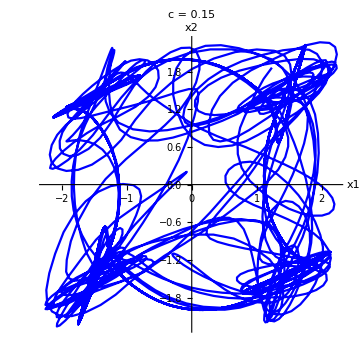
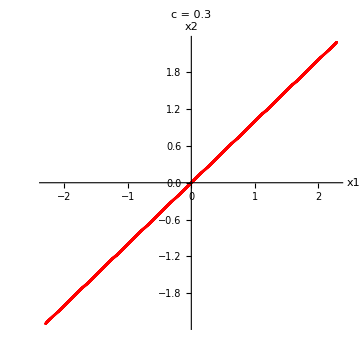

-Graphics-

-Graphics-

```mathematica
(*Parameters*)
c1=15.6;
c2=1;
c3=25.58;
m0=-8/7;
m1=-5/7;
T=400;

f[{x_,y_,z_}]:={c1 (y-x-g[x]),c2 (x-y+z),-c3 y};

(*First solution with c=0.15*)
c=0.15;
coupEqns=Join[{x1'[t]==f[{x1[t],y1[t],z1[t]}][[1]]+c (x2[t]-x1[t]),y1'[t]==f[{x1[t],y1[t],z1[t]}][[2]]+c (y2[t]-y1[t]),z1'[t]==f[{x1[t],y1[t],z1[t]}][[3]]+c (z2[t]-z1[t]),x2'[t]==f[{x2[t],y2[t],z2[t]}][[1]]+c (x1[t]-x2[t]),y2'[t]==f[{x2[t],y2[t],z2[t]}][[2]]+c (y1[t]-y2[t]),z2'[t]==f[{x2[t],y2[t],z2[t]}][[3]]+c (z1[t]-z2[t])},{x1[0]==0.2,y1[0]==0.2,z1[0]==0.2,x2[0]==-0.2,y2[0]==-0.2,z2[0]==-0.2}];
sol1=NDSolve[coupEqns,{x1,y1,z1,x2,y2,z2},{t,0,T}];

(*Second solution with c=0.3*)
c=0.30;
coupEqns=Join[{x1'[t]==f[{x1[t],y1[t],z1[t]}][[1]]+c (x2[t]-x1[t]),y1'[t]==f[{x1[t],y1[t],z1[t]}][[2]]+c (y2[t]-y1[t]),z1'[t]==f[{x1[t],y1[t],z1[t]}][[3]]+c (z2[t]-z1[t]),x2'[t]==f[{x2[t],y2[t],z2[t]}][[1]]+c (x1[t]-x2[t]),y2'[t]==f[{x2[t],y2[t],z2[t]}][[2]]+c (y1[t]-y2[t]),z2'[t]==f[{x2[t],y2[t],z2[t]}][[3]]+c (z1[t]-z2[t])},{x1[0]==0.2,y1[0]==0.2,z1[0]==0.2,x2[0]==-0.2,y2[0]==-0.2,z2[0]==-0.2}];
sol2=NDSolve[coupEqns,{x1,y1,z1,x2,y2,z2},{t,0,T}];

(*Plotting*)
plot1=ParametricPlot[Evaluate[{x1[t],x2[t]}/. sol1],{t,0.5*T,T},AxesLabel->{"x1","x2"},PlotStyle->Blue,PlotRange->All,ImageSize->Medium,PlotLabel->"c = 0.15"];
plot2=ParametricPlot[Evaluate[{x1[t],x2[t]}/. sol2],{t,0.5*T,T},AxesLabel->{"x1","x2"},PlotStyle->Red,PlotRange->All,ImageSize->Medium,PlotLabel->"c = 0.3"];

{plot1,plot2}
plot1
plot2
```